```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Rct_tracingdelay",date,".pdf"],figuretracingdelay,"pdf"];
```

# A model for the spread of corona virus: R0

```mathematica
date=DateString[{"Day","Month","YearShort"}]
```

070520

```mathematica
AspRat=0.75;
ImSize=400;
```

## Model Parameters

## Biological parameters

```mathematica
meanhouseholdcontacts=4.0;negbinn=1.6;negbinp=0.15;
```

duration of the latent and infectious periods, casefatality, and ratio of transmission probabilities in 2. ring to 1. ring contacts:

```mathematica
latent=3;infectious=10;casefatality=0.02; 
transratio=0.25;declinetransm=0.5;
transmissibility=0.1211;
sympconstant=4.0;gamma1=8.0;gamma2=0.7;
scenariocontactred={1.0,0.95,0.9,0.85,0.8,0.75,0.7,0.65,0.6,0.55,0.5,0.45,0.4,0.35,0.3,0.25,0.2,0.15,0.1,0.05};fractionapp=1.0;fractest=1.0;
```

```mathematica
calcsymp[x_]=Total[Table[Product[(1-x*sympconstant*PDF[GammaDistribution[gamma1,gamma2],j-1]),{j,2,i}]*x*sympconstant*PDF[GammaDistribution[gamma1,gamma2],i],{i,1,infectious}]];
scenarioasymptomatic=Table[FindRoot[calcsymp[x]==1-0.05*(i-1),{x,0.5}],{i,1,20}][[All,1,2]];
```

```mathematica
factorasymptomatic=scenarioasymptomatic[[5]]
```

0.361425

```mathematica
contactreduction1=scenariocontactred[[9]]
```

0.6

```mathematica
contactreduction2=scenariocontactred[[15]]
```

0.3

probability of leaving latent stage by time since infection:

```mathematica
probinf=Array[f,latent];
probinf=Flatten[Append[Table[0.0,{i,1,latent-3}],{0.5,0.7,1.0}]]
```

{0.5,0.7,1.}

probability of transmission per contact by time since beginning of infectious period:

```mathematica
probtransm[pt_]=Table[Min[1.0,pt*tau*Exp[-tau*declinetransm]], {tau,1,infectious}]//N;
```

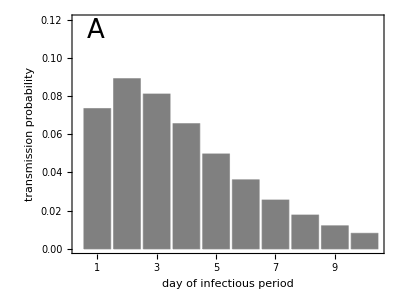

```mathematica
figure1a=Show[BarChart[probtransm[transmissibility],AspectRatio->AspRat,ImageSize->ImSize,PlotRange->{All,{0.0,0.12}},ChartStyle->GrayLevel[0.5],Frame->True, FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}, FrameStyle->Directive[Black,17],FrameLabel->{"day of infectious period", "transmission probability"}],Graphics[Text[StyleForm["A",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(10.0-0.5)*0.1,0.12*0.95}]]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_1A_",date,".pdf"],figure1a,"pdf"];
```

probability of developing symptoms by time since becoming infectious:

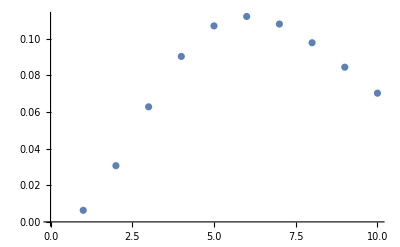

```mathematica
ListPlot[Table[PDF[GammaDistribution[4,2],i],{i,1,infectious}]]
```

```mathematica
probsymp=Table[ factorasymptomatic*sympconstant*PDF[GammaDistribution[gamma1,gamma2],i],{i,1,infectious}];
```

```mathematica
probdevelopingsymptoms=Table[Product[(1-probsymp[[j-1]]),{j,2,i}]*probsymp[[i]],{i,1,infectious}];
```

```mathematica
fraccas=Total[probdevelopingsymptoms]
```

0.8

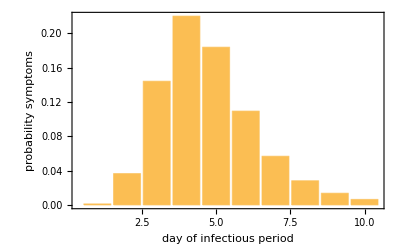

```mathematica
plotprobsymptoms=BarChart[probdevelopingsymptoms, Frame->True,ChartLabels->Table[i,{i,1,infectious}],FrameLabel->{"day of infectious period", "probability symptoms"},FrameTicks->{{True,None},{True,None}},FrameStyle->Directive["Label",16]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Probsymptoms_",date,".pdf"],plotprobsymptoms,"pdf"];
```

distribution of the number of contacts with susceptibles by time since beginning of the infectious period:

```mathematica
saturation1=Drop[Prepend[Table[Product[1-probtransm[transmissibility][[j]],{j,1,i}],{i,1,infectious}],1.0],-1]
```

{1.,0.926549,0.843993,0.775576,0.724732,0.688711,0.663797,0.646805,0.635328,0.627636}

```mathematica
saturation2=Drop[Prepend[Table[Product[1-probtransm[transmissibility*transratio][[j]],{j,1,i}],{i,1,infectious}],1.0],-1]
```

{1.,0.981637,0.959771,0.940321,0.92491,0.913417,0.905156,0.899364,0.895374,0.892664}

```mathematica
BarChart[saturation1,ChartLabels->Table[i,{i,1,infectious}]];
```

```mathematica
mu1=meanhouseholdcontacts*saturation1*contactreduction1
```

{2.4,2.22372,2.02558,1.86138,1.73936,1.65291,1.59311,1.55233,1.52479,1.50633}

```mathematica
mu2=negbinn*saturation2*contactreduction2
```

{0.48,0.471186,0.46069,0.451354,0.443957,0.43844,0.434475,0.431695,0.42978,0.428479}

```mathematica
contactdist1=Array[f,infectious];contactdist2=Array[f,infectious];
For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}];
```

```mathematica
contact=Array[f,latent+infectious];
For [i=1,i≤infectious,i++,contact[[i]]=Mean[contactdist1[[i]]]+Mean[contactdist2[[i]]]]
```

```mathematica
numcontacts=Table[RandomVariate[contactdist1[[i]],1000]+RandomVariate[contactdist2[[i]],1000],{i,1,infectious}];
```

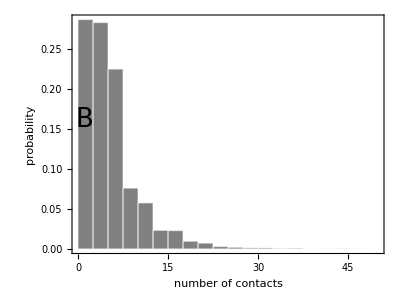

```mathematica
figure1b=Show[Histogram[RandomVariate[PoissonDistribution[meanhouseholdcontacts*contactreduction1],10000]+RandomVariate[NegativeBinomialDistribution[negbinn*contactreduction2,negbinp],10000], {0, 50, 2.5},"Probability", ChartBaseStyle->EdgeForm[White],AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"number of contacts", "probability"},FrameTicks->{{True,None},{True,None}}],Graphics[Text[StyleForm["B",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(12.0-0.5)*0.1,0.17*0.95}]]]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Figure_1B_",date,".pdf"],figure1b,"pdf"];
```

```mathematica
meancontacts=Table[Mean[numcontacts[[i]]],{i,1,infectious}]//N
```

{4.893,4.883,4.693,4.413,4.421,3.953,4.154,4.006,3.834,3.958}

```mathematica
plotmeancontacts=BarChart[meancontacts, ChartLabels->Table[i,{i,1,infectious}],AxesLabel->{"day infectious period","mean number of contacts with susceptibles"}];
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/Figures/Meancontacts_",date,".pdf"],plotmeancontacts,"pdf"];
```

```mathematica
stdcontacts=Table[StandardDeviation[numcontacts[[i]]],{i,1,infectious}]//N
```

{4.52571,4.48859,4.78159,4.34042,4.43999,4.16295,4.30637,4.69915,4.12522,4.29496}

```mathematica
ListPlot[stdcontacts];
```

basic reproduction ratio:

```mathematica
rzero[pt_]:=∑_(i=1)^infectious (Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]])
```

```mathematica
Plot[rzero[x],{x,0,0.2},GridLines->{None,{2.5}}];
```

```mathematica
rzero1[pt_]:=∑_(i=1)^infectious Mean[contactdist1[[i]]]*probtransm[pt][[i]]
```

```mathematica
rzero2[pt_, tr_]:=∑_(i=1)^infectious Mean[contactdist2[[i]]]*probtransm[tr*pt][[i]]
```

```mathematica
rzero1[transmissibility]
```

0.905966

```mathematica
rzero2[transmissibility, transratio]
```

0.296907

```mathematica
rzero1[transmissibility]+rzero2[transmissibility,transratio]
```

1.20287

```mathematica
ratiohousehold[pt_, tr_]:=rzero1[pt]/(rzero1[pt]+rzero2[pt,tr]);
```

```mathematica
ratiohousehold[transmissibility, transratio]
```

0.753168

```mathematica
rzeroday[pt_]:=Table[Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[pt][[i]]*transratio, {i,1,infectious}]
```

```mathematica
rzeroperc=rzeroday[transmissibility]/rzero[transmissibility]*100
```

{18.8074,21.4162,18.0489,13.6293,9.78575,6.83894,4.70016,3.19208,2.14765,1.43358}

```mathematica
rzerocum=Table[∑_(i=1)^j rzeroperc[[i]], {j,1,infectious}];
```

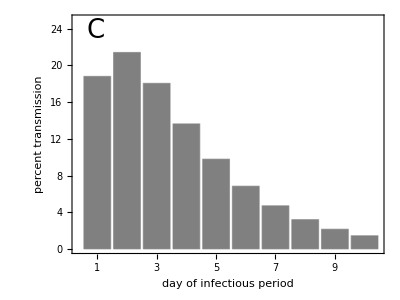

```mathematica
figure1c=Show[BarChart[rzeroperc,  AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],PlotRange->{All,{0,25}},Frame->True, FrameLabel->{"day of infectious period", "percent transmission"},FrameStyle->Directive[Black,17],  FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}],Graphics[Text[StyleForm["C",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(10.0-0.5)*0.1,25*0.95}]]]
```

## Exponential growth rate and doubling time

```mathematica
startinf=Table[Product[(1-probinf[[k-1]]),{k,2,j}]*probinf[[j]],{j,1,latent}]
```

{0.5,0.35,0.15}

```mathematica
generations[r_,pt_]:=Sum[Sum[Exp[-r*(i+j)]*startinf[[j]](Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]),{i,1,infectious}],{j,1,latent}]
```

```mathematica
expgrowth[pt_]:=FindRoot[generations[r,pt]==1,{r,1}][[1,2]]
```

```mathematica
unconstrainedgrowth=expgrowth[transmissibility]
```

0.0363759

```mathematica
doublingtime[pt_]:=Log[2]/expgrowth[pt];
```

```mathematica
unconstraineddoubtime=doublingtime[transmissibility]
```

19.0551

## Definition of vaccination and quarantine parameters

```mathematica
timewindow=7;
```

probability of being diagnosed by day since first symptoms for the first index case:

```mathematica
probdiag=Table[Table[If[i<ds ,0.0,fractest*probsymp[[i-ds+1]]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
probdiag[[1]]
```

{0.00119246,0.036579,0.149779,0.268906,0.307291,0.263875,0.186039,0.113535,0.0620548,0.0310926}

```mathematica
probbeingdiagnosed=Table[Table[Product[(1-probdiag[[ds,j-1]]),{j,2,i}]*probdiag[[ds,i]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
Total[Transpose[probbeingdiagnosed]][[1]]
```

0.8

```mathematica
probdiagapp[fa_]=Table[Table[If[i<ds ,0.0,fa*probsymp[[i-ds+1]]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
cumprobbeingdiagnosed=Table[Table[Sum[probbeingdiagnosed[[j,k]],{k,1,i}],{i,1,infectious}],{j,1,infectious}];
```

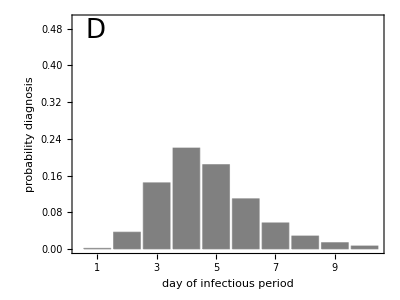

```mathematica
figure1d=Show[BarChart[probbeingdiagnosed[[1]], PlotRange->{All,{0,0.5}}, AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5], FrameStyle->Directive[Black,17],Frame->True, FrameLabel->{"day of infectious period", "probability diagnosis"},FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}],Graphics[Text[StyleForm["D",FontSize->26],{(10.0-0.5)*0.1,0.5*0.95}]]]
```

contact tracing and vaccination:

probability of being diagnosed on day i, if one has not been diagnosed up to day j (i>j):

```mathematica
pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
```

```mathematica
sums=Table[∑_(k=1)^(infectious-j) pd[[1,j,k]],{j,1,infectious-1}]
```

{0.799761,0.792159,0.755544,0.66563,0.517301,0.34427,0.194396,0.0912179,0.0310926}

```mathematica
BarChart[sums, ChartStyle->{GrayLevel[0.8]},ChartLabels->Table[i,{i,1,infectious}],Frame->True, FrameLabel->{"day of infectious period", "probability diagnosis"},FrameTicks->{Automatic,Automatic,None,None}];
```

```mathematica
rzerodayprob=rzeroday[transmissibility]/rzero[transmissibility]
```

{0.188074,0.214162,0.180489,0.136293,0.0978575,0.0683894,0.0470016,0.0319208,0.0214765,0.0143358}

```mathematica
cumrzerodayprob=Table[Sum[rzerodayprob[[j]],{j,1,i}],{i,1,infectious}]
```

{0.188074,0.402236,0.582725,0.719018,0.816876,0.885265,0.932267,0.964188,0.985664,1.}

```mathematica
transmissionweights=PadRight[1-Total[Table[startinf[[k]]*PadLeft[Drop[cumrzerodayprob,-k],infectious],{k,1,latent}]],infectious+timewindow]
```

{1.,0.905963,0.733056,0.539644,0.376202,0.252497,0.163608,0.101492,0.0588229,0.0298621,0,0,0,0,0,0,0}

probability of a contact being isolated by day since first symptoms of source (probtrace2: source is secondary case, contact is ring 1; probtrace3: source is secondary case, contact is ring 2):

```mathematica
probtrace[vd_,cv_,fa_]:=fa*Table[Flatten[{Table[∑_(j=i)^Min[i-1+Length[pd[[ds,i]]],i+timewindow] pd[[ds,i,j-i+1]]*cv*transmissionweights[[j+vd-1]],{i,1,infectious-1}],0}],{ds,1,infectious}];
```

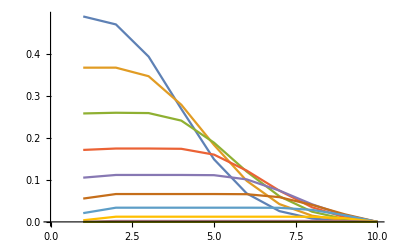

```mathematica
ListPlot[probtrace[1,1,1],Joined->True]
```

```mathematica
Mean[WeibullDistribution[3,7.2]]//N
```

6.42945

```mathematica
StandardDeviation[WeibullDistribution[3,7.2]]//N
```

2.33676

```mathematica
plotweibull=Plot[PDF[WeibullDistribution[3,7.2],x],{x,0,10}];
```

```mathematica
plotincubation=ListPlot[Total[Table[startinf[[k]]*PadLeft[Drop[probdevelopingsymptoms,-k],infectious],{k,1,latent}]],PlotMarkers->"OpenMarkers",PlotStyle->Red];
```

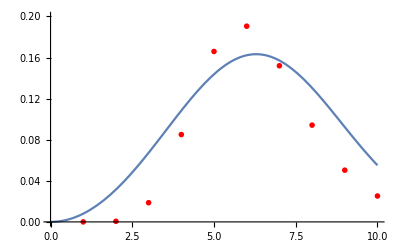

```mathematica
Show[plotweibull,plotincubation,PlotRange->{All,{0,0.2}}]
```

effective reproduction ratio with diagnosis probability  as above for all infecteds:

```mathematica
reffiso[pt_,ds_]:=∑_(i=1)^infectious ((Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

effective reproduction ratio with contact tracing:

```mathematica
reffvacc1[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=∑_(i=1)^infectious (Mean[contactdist1[[i]]]*probtransm[pt][[i]]*(1-probtrace[vd1,cv1,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

```mathematica
reffvacc2[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=∑_(i=1)^infectious ( Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]*(1-probtrace[vd2,cv2,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

```mathematica
reffvacc[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=reffvacc1[pt,vd1,vd2,cv1,cv2,ds,fa]+reffvacc2[pt,vd1,vd2,cv1,cv2,ds,fa]
```

## Exponential growth rate and doubling time

```mathematica
generationseff[r_,pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=∑_(i=1)^infectious Sum[Exp[-r*(i+k)]*startinf[[k]]*((Mean[contactdist1[[i]]]*probtransm[pt][[i]]*(1-probtrace[vd1,cv1,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))+( Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]*(1-probtrace[vd2,cv2,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))),{k,1,latent}];
```

```mathematica
expgrowtheff[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=FindRoot[generationseff[r,pt,vd1,vd2,cv1,cv2,ds,fa]==1,{r,1}][[1,2]]
```

```mathematica
doublingtimeeff[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=Log[2]/expgrowtheff[pt,vd1,vd2,cv1,cv2,ds,fa];
```

## Specific parameter values

```mathematica
vaccdelay2=1.0;vaccdelay3=1.0;coverage2=1.0; coverage3=1.0;diagdelay=1; colorscheme=10;
```

```mathematica
reffiso[transmissibility,diagdelay]
```

0.967089

```mathematica
reffvacc1[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractest]
```

0.456034

```mathematica
reffvacc2[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractest]
```

0.147438

```mathematica
reffvacc[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractest]
```

0.603472

```mathematica
doubeff=doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractest]
```

-6.9416

```mathematica
doubincrease=doubeff/unconstraineddoubtime
```

-0.364291

```mathematica
legend3=LineLegend[ Table[RGBColor[(k-1) 0.2,0.2( k-1),1],{k,{1,2,3,4}}],Table[j,{j,{0,1,2,3}}],LegendLabel->"D_2 (days)",LabelStyle->Directive[Black,14], LegendMargins->5]
```

```mathematica
labelgraph="Fraction symptomatic tested ";
```

```mathematica
yrange={0.5,1.3};
```

```mathematica
figure1= Show[Table[ListPlot[Table[{dd-1,reffvacc[transmissibility,k,k,coverage2,coverage3,dd,fractest]},{dd,1,8}],PlotRange->{All,yrange},Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{RGBColor[0.2*(k-1),0.2*(k-1),1],Thickness[0.01]},GridLines->{None,{{rzero[transmissibility],{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,cts]],None},{"diagnosis delay D_1 (days)" ,StringJoin[labelgraph,ToString[Ceiling[fractest*100]],"%"]}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],{k,{1,2,3,4}}],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,rzero[transmissibility]+0.04}]],Graphics[Inset[legend3,{6.0,0.8}]]];
```

```mathematica
covvalues={1,3,5,7}
```

{1,3,5,7}

```mathematica
legend4=LineLegend[ Table[RGBColor[(k-1) 0.1,0.1( k-1),1],{k,covvalues}],Table[NumberForm[1*(1-(j-1)*0.1),{2,1}],{j,covvalues}],LegendLabel->"Coverage",LabelStyle->Directive[Black,14], LegendMargins->5]
```

```mathematica
figure2= Show[Table[ListPlot[Table[{dd-1,reffvacc[transmissibility,vaccdelay2,vaccdelay3,fractionapp*(1-(k-1)*0.1),fractionapp*(1-(k-1)*0.1),dd,fractest]},{dd,1,8}],PlotRange->{All,yrange},Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{RGBColor[0.1*(k-1),0.1*(k-1),1],Thickness[0.01]},GridLines->{None,{{rzero[transmissibility],{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,cts]],None},{"diagnosis delay D_1 (days)" ,StringJoin[labelgraph,ToString[Ceiling[fractest*100]],"%"]}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],{k,covvalues}],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,rzero[transmissibility]+0.04}]],Graphics[Inset[legend4,{6.0,0.8}]]];
```

```mathematica
figure3= Show[ListPlot[Table[{dd-1,reffvacc[transmissibility,vaccdelay2,vaccdelay3,0,0,dd,fractest]},{dd,1,8}],PlotRange->{All,yrange},Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{RGBColor[0.0,0.4,0.0],Thickness[0.01]},LabelStyle->{RGBColor[0,0.4,0],14},PlotLabels->Placed["isolation",{Scaled[0.12],Top}],GridLines->{None,{{rzero[transmissibility],{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,cts]],None},{"diagnosis delay D_1 (days)" ,None}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,rzero[transmissibility]+0.04}]]];
```

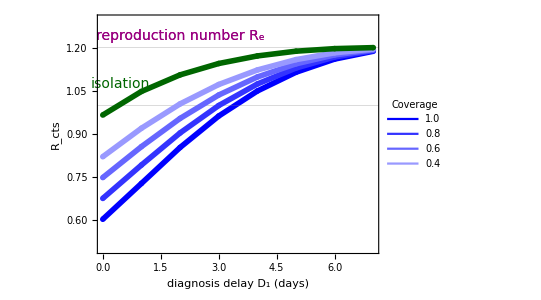

```mathematica
figurecoverage=Show[figure2,figure3,FrameTicks->{{Automatic,None},{Automatic,None}}]
```

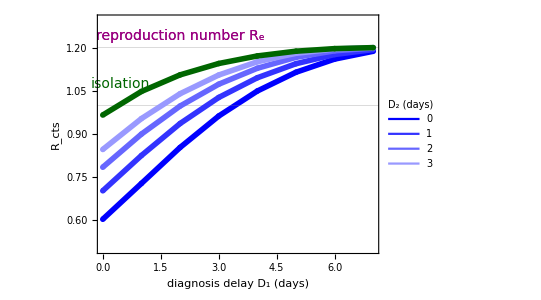

```mathematica
figuretracingdelay=Show[figure1,figure3,FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
legend1=LineLegend[{RGBColor[1, 0.49, 0],RGBColor[0.2, 0.2, 1], RGBColor[0,0.8,1]},{ "Conventional CT","Mobile App CT 100%", "Mobile App CT 80%"},LegendLabel->"CTS",LabelStyle->Directive[GrayLevel[0],14],LegendMargins->5]
```

```mathematica
figure4= Show[ListPlot[{Table[{dd-1,reffvacc[transmissibility,1,1,1,1,dd,1]},{dd,1,8}],Table[{dd-1,reffvacc[transmissibility,1,1,0.8,0.8,dd,0.8]},{dd,1,8}],Table[{dd-1,reffvacc[transmissibility,4,4,0.8,0.5,dd,fractest]},{dd,1,10}]},PlotRange->{All,yrange},Joined->True,PlotMarkers->"OpenMarkers",PlotStyle->{{RGBColor[0.0,0.0,1],Thickness[0.01]},{RGBColor[0,0.8,1],Thickness[0.01]},{RGBColor[1,0.5,0.0],Thickness[0.01]}},GridLines->{None,{{rzero[transmissibility],{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,ct]],None},{"diagnosis delay D_1 (days)" ,StringJoin[labelgraph,ToString[Ceiling[fractionapp*100]],"%"]}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,rzero[transmissibility]+0.04}]],Graphics[Inset[legend1,{5.0,0.8}]]];
```

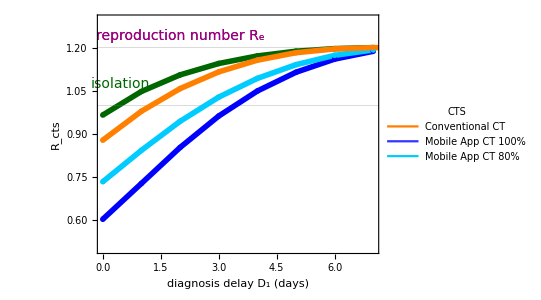

```mathematica
Show[figure3,figure4]
```

```mathematica
xvalues=Table[rzero[x],{x,0.05,0.1,0.01}];
```

```mathematica
yvalues1=Table[reffiso[x,1],{x,0.05,0.1,0.01}];
```

```mathematica
yvalues2=Table[reffvacc[x,1,1,1.0,1.0,1],{x,0.05,0.1,0.01}];
```

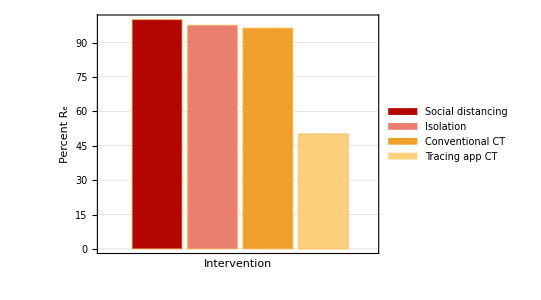

```mathematica
figure5=BarChart[{100,reffiso[transmissibility,5]/rzero[transmissibility]*100,reffvacc[transmissibility,4,4,0.8,0.5,5,fractest]/rzero[transmissibility]*100,reffvacc[transmissibility,1,1,fractionapp,fractionapp,1,fractionapp]/rzero[transmissibility]*100},PlotRange->{All,{0,100}},GridLines->{None,Automatic},ChartStyle->colorscheme, ChartLegends->{"Social distancing","Isolation","Conventional CT","Tracing app CT"},Frame->True,FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},FrameLabel->{"Intervention","Percent R_e"},AspectRatio->AspRat,ImageSize->ImSize]
```

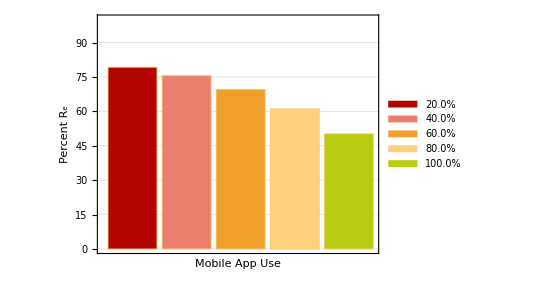

```mathematica
figure6=BarChart[Table[reffvacc[transmissibility,1,1,k*0.2,k*0.2,1,k*0.2]/rzero[transmissibility]*100,{k,1,5}],PlotRange->{All,{0,100}},GridLines->{None,Automatic},ChartStyle->colorscheme, ChartLegends->{Table[StringJoin[ToString[NumberForm[(k*0.2)*100,{3,1}]],"%"],{k,1,5}]},Frame->True,FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},FrameLabel->{"Mobile App Use","Percent R_e"},AspectRatio->AspRat,ImageSize->ImSize]
```

```mathematica
result={};
Do[probdiag=probdiagapp[k*0.2];result=Append[result,reffvacc[transmissibility,1,1,k*0.2,k*0.2,1,k*0.2]/rzero[transmissibility]*100],{k,1,5}]
```

```mathematica
result
```

{93.7552,85.6328,75.65,63.8235,50.1693}

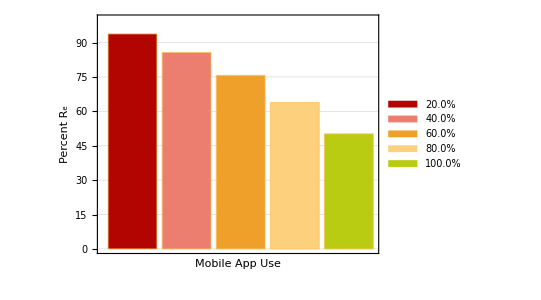

```mathematica
figure7=BarChart[result,PlotRange->{All,{0,100}},GridLines->{None,Automatic},ChartStyle->colorscheme, ChartLegends->{Table[StringJoin[ToString[NumberForm[(k*0.2)*100,{3,1}]],"%"],{k,1,5}]},Frame->True,FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},FrameLabel->{"Mobile App Use","Percent R_e"},AspectRatio->AspRat,ImageSize->ImSize]
```

## Transmission prevented per diagnosed case

```mathematica
factorasymptomatic=scenarioasymptomatic[[1]]
```

1.17617

```mathematica
probsymp=Table[ factorasymptomatic*sympconstant*PDF[GammaDistribution[gamma1,gamma2],i],{i,1,infectious}];
```

```mathematica
probdiag=Table[Table[If[i<ds ,0.0,fractest*probsymp[[i-ds+1]]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
```

```mathematica
preventedisolation=Table[(rzero[transmissibility]-reffiso[transmissibility,ds])/rzero[transmissibility]*100,{ds,1,infectious-3}]
```

{37.3403,25.0511,16.2233,10.0553,5.81889,2.94376,1.06411}

```mathematica
preventedct=Table[Table[(rzero[transmissibility]-(reffvacc1[transmissibility,vd,vd,1,1,ds,1]+reffvacc2[transmissibility,vd,vd,1,1,ds,1]))/rzero[transmissibility]*100,{ds,1,infectious-3}],{vd,1,5}];
```

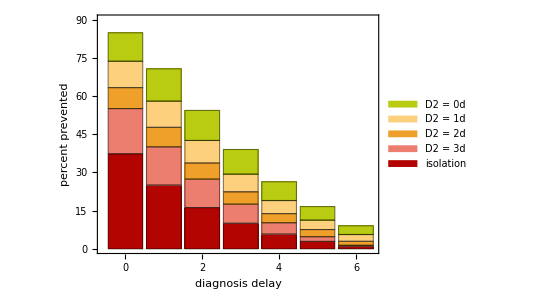

```mathematica
plottransmissionprevented=BarChart[Transpose[{preventedisolation,preventedct[[4]]-preventedisolation,preventedct[[3]]-preventedct[[4]],preventedct[[2]]-preventedct[[3]],preventedct[[1]]-preventedct[[2]]}],ChartLayout->"Stacked",PlotRange->{All,{0,90}}, AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->colorscheme,  ChartLegends->{"isolation","D2 = 3d","D2 = 2d","D2 = 1d", "D2 = 0d"},FrameStyle->Directive[Black,17],Frame->True, FrameLabel->{"diagnosis delay", "percent prevented"},FrameTicks->{{True,None},{Table[{i,i-1},{i,1,infectious-3}],None}}]
```

## Output

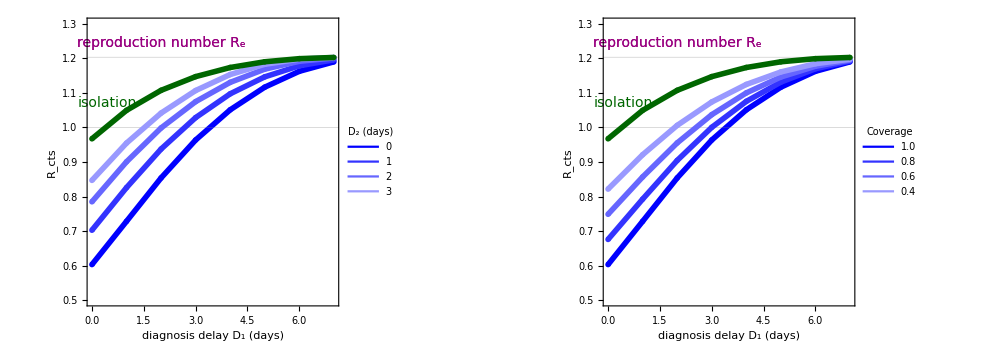

```mathematica
figurepaper1=Show[GraphicsRow[{figuretracingdelay,figurecoverage}], GraphicsSpacing->0.01,ImageSize->2.5*ImSize,FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/CoronaApp/Figures/Figure2_",date,".pdf"],figurepaper1,"pdf"];
```

```mathematica
figurepaper2=Show[figure3,figure4,ImageSize->ImSize,FrameTicks->{Automatic, Automatic, None, None}]
```

-Graphics-

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/CoronaApp/Figures/Figure3_",date,".pdf"],figurepaper2,"pdf"];
```

```mathematica
figurepaper3=Show[figure5,ImageSize->ImSize,FrameTicks->{None, Automatic, None, None}]
```

-Graphics-

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/CoronaApp/Figures/Figure4_",date,".pdf"],figurepaper3,"pdf"];
```

```mathematica
figurepaper4=Show[figure6,FrameTicks->{None, Automatic, None, None}]
```

-Graphics-

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/CoronaApp/Figures/Figure5a_",date,".pdf"],figurepaper4,"pdf"];
```

```mathematica
figurepaper5=Show[figure7,FrameTicks->{None, Automatic, None, None}]
```

-Graphics-

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/CoronaApp/Figures/Figure5b_",date,".pdf"],figurepaper5,"pdf"];
```

```mathematica
figurepaper6=Show[plottransmissionprevented]
```

-Graphics-

```mathematica
Export[StringJoin["/Users/avalon/Projects/Corona/CoronaApp/Figures/Figure6_",date,".pdf"],figurepaper6,"pdf"];
```